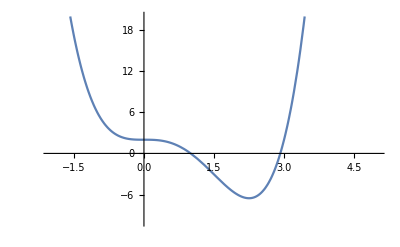

```mathematica
Plot[x^4-3*x^3+2,{x,-2,5},PlotRange->{-10,20}]
```

```mathematica
Clear["`*"]
f[x_]:=x^4-3*x^3+2;
grad[x_]:=-9*x^2+4*x^3;
grad2[x_]:=-18*x+12*x^2;
initial=1.6;
maxiter=200;
tol=10.^-10;
alpha=0.02;
```

```mathematica
val=Infinity;
count=0;
Do[
initial=initial-grad[initial]/(grad2[initial]+10.^-6);
(*initial=initial-alpha*grad[initial];*)
valnew=f[initial];
diff=valnew-val;
If[Abs[diff]<=tol,Break[]];
val=valnew;
count++;
,{i,maxiter}];
count
diff<=10.^-10
val
initial
```

7

True

-6.54297

2.25